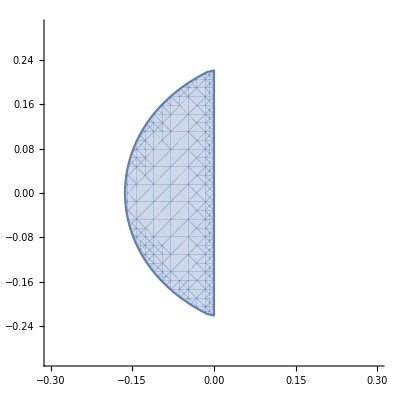

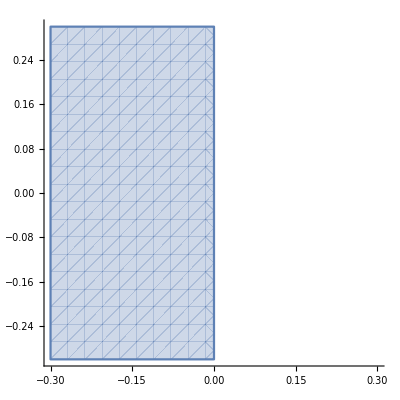

```mathematica
(****  Fifth-Order Adams Bashforth Method ****)
pAB5[z_]:= z^5-z^4;
qAB5[z_]:=(1901z^4-2774z^3+2616z^2-1274z+251)/720;

(****  Fifth-Order Adams Moulton Method ****)
pAM5[z_]:= z^5-z^4;
qAM5[z_]:= (251z^5+646z^4-264z^3+106z^2-19z)/720;

w[x_,y_]:=x+I y;
tAB5[x_,y_]:=NSolve[pAB5[z]-w[x,y] qAB5[z]==0,z];
tAM5[x_,y_]:=NSolve[pAM5[z]-w[x,y] qAM5[z]==0,z];

RegionPlot[
Max[Abs[z]/.tAB5[x,y]]≤1,{x,-0.3,0.3},{y,-0.3,0.3},Frame->None,Axes->True
]
RegionPlot[
Max[Abs[z]/.tAM5[x,y]]≤1,{x,-0.3,0.3},{y,-0.3,0.3},Frame->None,Axes->True
]
```